```mathematica
NestWhile[{Piecewise[{{Abs[#[[1]]-(3/4)^(#[[4]])], #[[1]]≥#[[2]]}, {#[[1]], #[[1]]<#[[2]]}}],Piecewise[{{Abs[#[[2]]-(3/4)^(#[[4]])], #[[2]]≥#[[1]]}, {#[[2]], #[[2]]<#[[1]]}}],(#[[1]])/(#[[2]]),#[[4]]+1}&,{3,5,3/5,1},Abs[(#[[3]]-0.00001)]>0&,1,100]
```

{4017345110648288730275723699355313940418665331882080572291695/1606938044258990275541962092341162602522202993782792835301376,1004336277662052194999070699085902113895411625212497481695297/401734511064747568885490523085290650630550748445698208825344,1004336277662201026949113927671587600387107738288695669953424/1004336277662052194999070699085902113895411625212497481695297,101}

```mathematica
N[%,1000]
```

{2.50000000000050595691832872592113272251108153631312118418876711385646726199026302542648327597135642471669133980494042066392969854496923446452152724348970769057375063137982351690880022943019866943359375,2.500000000000456203737285725223068429895887671007513705318017421725311582363492047513806170540815494889869214955143081915169938481126035268132646173888278978182653222717135577113367617130279541015625,1.00000000000014818935983243338996995808624242615310679389479009431826266441457587866614504971594506933512686764227127973377161484426438113650778783748089848850173382602910704937352273684665753352242318295171452564174496215355311659871070546569822117994476583038130251267119519005265446621644918474513058995102067101054772821484401879367987753958471913643232903016735801163826040988705194461147334672955278362789808125569760311213182162182377004087839829052418368654476541575344423647536049988571574028980250775094104995363578154312450939855678893628008296697610539860972231781292075526152652717035066347700435810680370454888728252556341176651499283625958210335735955604902315986207810864475888464547215022586716508670986556619665052744354973774909564533608611832880554407732052425173087418655020484858785674775272719212559547974352709807606211056772375170024120902307587967006508069937249298049468438280229022001465581010266990933705400600542405774810732969298594534390465765607062816161726569980408,101.}

```mathematica
∑_(i=1)^∞ (3/4)^i//N
```

3.

```mathematica
N[%[[1]],10]
```

0.00004999

```mathematica
NestWhile[{Piecewise[{{Abs[#[[1]]-1/(#[[4]])], #[[1]]≥#[[2]]}, {#[[1]], #[[1]]<#[[2]]}}],Piecewise[{{Abs[#[[2]]-1/(#[[4]])], #[[2]]≥#[[1]]}, {#[[2]], #[[2]]<#[[1]]}}],(#[[1]])/(#[[2]]),#[[4]]+1}&,{3,10,3/5,1},(#[[3]]-0.0001)>0&,1,1000]
```

{599264867322240469052155271755652333682380562979361220212323228692914042013992397023550282234932385823278502835936518058839094672253179297444510640797484319541205168569158953908968832749069739508325343230331043099373153835699714721430685606993824039401426607288186444270892224870328392281524769421424643553/217302417257559953937241467692553838748808074901133425655748031353994757800064351834615590943009839663597070772631201607153331427641905863297497867002658574822769302364046653706395724994254400061869245764432215545465617561546871196257609132272623789825634797378138780385831136027228504886268850258871916875,5102818411086404309012159843740707251339600716973567610737086423608934914500037304860231479267360685123370038745531709276429336939522376800279949459089555700911455628995879220335538915036759221606544355070883061642916088502573141391168760572384570068606015208556659/1851004635935800314837319405732223101528870745112227549207393210427987423057186410534204310356860730203045891594645101125307156037826651744216154279143292927411896573007031825507916271132221755840779223201088203336026920937635142038125021027270521082695835911744000,19659599542865548500921710189794190532686340391524533809013814532897724514758580227084166604557114495153463701095019846528836818181392303736963179013500099018647828288547238960636680867768447417044865532404175031525337392670154021561680187086457045720009822886758791391605715087455766288617251284396914026113185008426020664684185044287828355448260750626119115176511031711569018664701026651019993722493215725242496742498899134385253888/19659864610760541237703404594604091299270520891469701512801314105643374058386348620102985912490094314876690906426009965017977422843863428077042265586904887555246065415565665084240964750950495729321367360618311396194376463218986810634303788469618631329614184260648844417879497866306971565052645209161681242875965015194466121202289246820342704026042432478414975420733130561639673868945478846106326779667205682848693834833985419260587115,1001}

```mathematica
N[19659599542865548500921710189794190532686340391524533809013814532897724514758580227084166604557114495153463701095019846528836818181392303736963179013500099018647828288547238960636680867768447417044865532404175031525337392670154021561680187086457045720009822886758791391605715087455766288617251284396914026113185008426020664684185044287828355448260750626119115176511031711569018664701026651019993722493215725242496742498899134385253888/19659864610760541237703404594604091299270520891469701512801314105643374058386348620102985912490094314876690906426009965017977422843863428077042265586904887555246065415565665084240964750950495729321367360618311396194376463218986810634303788469618631329614184260648844417879497866306971565052645209161681242875965015194466121202289246820342704026042432478414975420733130561639673868945478846106326779667205682848693834833985419260587115]
```

0.999987

```mathematica
FindInstance[1/3==x/9^y,{x,y},Integers]
```

```mathematica
Table[{1/3 9^y==x,x,y},{x,1,10},{y,1,10}]
```

{{{False,1,1},{False,1,2},{False,1,3},{False,1,4},{False,1,5},{False,1,6},{False,1,7},{False,1,8},{False,1,9},{False,1,10}},{{False,2,1},{False,2,2},{False,2,3},{False,2,4},{False,2,5},{False,2,6},{False,2,7},{False,2,8},{False,2,9},{False,2,10}},{{True,3,1},{False,3,2},{False,3,3},{False,3,4},{False,3,5},{False,3,6},{False,3,7},{False,3,8},{False,3,9},{False,3,10}},{{False,4,1},{False,4,2},{False,4,3},{False,4,4},{False,4,5},{False,4,6},{False,4,7},{False,4,8},{False,4,9},{False,4,10}},{{False,5,1},{False,5,2},{False,5,3},{False,5,4},{False,5,5},{False,5,6},{False,5,7},{False,5,8},{False,5,9},{False,5,10}},{{False,6,1},{False,6,2},{False,6,3},{False,6,4},{False,6,5},{False,6,6},{False,6,7},{False,6,8},{False,6,9},{False,6,10}},{{False,7,1},{False,7,2},{False,7,3},{False,7,4},{False,7,5},{False,7,6},{False,7,7},{False,7,8},{False,7,9},{False,7,10}},{{False,8,1},{False,8,2},{False,8,3},{False,8,4},{False,8,5},{False,8,6},{False,8,7},{False,8,8},{False,8,9},{False,8,10}},{{False,9,1},{False,9,2},{False,9,3},{False,9,4},{False,9,5},{False,9,6},{False,9,7},{False,9,8},{False,9,9},{False,9,10}},{{False,10,1},{False,10,2},{False,10,3},{False,10,4},{False,10,5},{False,10,6},{False,10,7},{False,10,8},{False,10,9},{False,10,10}}}

```mathematica
NestWhileList[#+1&,0,1/3 9^(Unpair[#][[1]])≠Unpair[#][[2]]&,1,100]
```

{0,1,2,3,4,5,6,7,8,9,10,11}

```mathematica
Unpair[11]
```

{1,3}

```mathematica
Pair[x_,y_]:=(x^2+3x+2 x y+y+y^2)/2
```

```mathematica
Pair[0,0]
```

0

```mathematica
Pair[0,1]
```

1

```mathematica
Pair[1,0]
```

2

```mathematica
Pair[0,2]
```

3

```mathematica
Pair[1,1]
```

4

```mathematica
Unpair[z_]:=With[{i=Floor[(-1+√(1+8z))/2]},{z-(i(1+i))/2,(i(3+i))/2-z}]
```

```mathematica
Unpair[1]
```

{0,1}

```mathematica
Unpair[2]
```

{1,0}

```mathematica
Unpair[5]
```

```mathematica
1+{2,0}
```

{3,1}

```mathematica
FromDigits[
```

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11}}

```mathematica
1/3 9^({3,2}[[2]])≠{3,2}[[1]]
```

True

```mathematica
ProgressIndicator[Dynamic[n],{1,1000000}]
```

```mathematica
NestWhile[((n=#)&;#+1&),0,1/7 9^(Unpair[#][[1]])≠Unpair[#][[2]]&,1,1000000]
```

$Aborted

```mathematica
N[1/7,25]
```

0.1428571428571428571428571

```mathematica
142857/(10^6-1)
```

1/7

```mathematica
142857*7==10^6-1
```

True

```mathematica
FindInstance[{Mod[n*7,9]==0,n>0},n]
```

{{n→9}}

```mathematica
Log[7]/Log[9]//N
```

0.885622

```mathematica
First[RealDigits[1/7,10,10]]
```

{1,4,2,8,5,7,1,4,2,8}

```mathematica
First[RealDigits[1/17,10,20]]
```

{5,8,8,2,3,5,2,9,4,1,1,7,6,4,7,0,5,8,8,2}

```mathematica
N[1/17,20]
```

0.058823529411764705882

```mathematica
588235294117647/9999999999999999
```

1/17

```mathematica
MultiplicativeOrder[17,10]
```

4

```mathematica
a/b==x/(10^y-1)
```

```mathematica
10^y-1==b x
```

```mathematica
10^MultiplicativeOrder[10,b]-1==b x
```

```mathematica
Solve[10^6-1==7x,x]
```

{{x→142857}}

```mathematica
MultiplicativeOrder[10,7]
```

6

```mathematica
Table[Piecewise[{{Solve[10^MultiplicativeOrder[10,b]-1==b x,x], GCD[10,b]==1}, {0, GCD[10,b]≠1}}],{b,1,100}]
```

{{{x→9}},0,{{x→3}},0,0,0,{{x→142857}},0,{{x→1}},0,{{x→9}},0,{{x→76923}},0,0,0,{{x→588235294117647}},0,{{x→52631578947368421}},0,{{x→47619}},0,{{x→434782608695652173913}},0,0,0,{{x→37}},0,{{x→344827586206896551724137931}},0,{{x→32258064516129}},0,{{x→3}},0,0,0,{{x→27}},0,{{x→25641}},0,{{x→2439}},0,{{x→23255813953488372093}},0,0,0,{{x→212765957446808510638297872340425531914893617}},0,{{x→20408163265306122448979591836734693877551}},0,{{x→196078431372549}},0,{{x→188679245283}},0,0,0,{{x→17543859649122807}},0,{{x→169491525423728813559322033898305084745762711864406779661}},0,{{x→16393442622950819672131147540983606557377049180327868852459}},0,{{x→15873}},0,0,0,{{x→14925373134328358208955223880597}},0,{{x→144927536231884057971}},0,{{x→1408450704225352112676056338028169}},0,{{x→1369863}},0,0,0,{{x→12987}},0,{{x→126582278481}},0,{{x→12345679}},0,{{x→1204819277108433734939759036144578313253}},0,0,0,{{x→114942528735632183908045977}},0,{{x→1123595505617977528089887640449438202247191}},0,{{x→10989}},0,{{x→10752688172043}},0,0,0,{{x→10309278350515463917525773195876288659793814432989690721649484536082474226804123711340206185567}},0,{{x→1}},0}

```mathematica
Map[ToExpression[StringReplace[ToString[#],{"{{x -> "->"","}}"->""}]]&,%]
```

{9,0,3,0,0,0,142857,0,1,0,9,0,76923,0,0,0,588235294117647,0,52631578947368421,0,47619,0,434782608695652173913,0,0,0,37,0,344827586206896551724137931,0,32258064516129,0,3,0,0,0,27,0,25641,0,2439,0,23255813953488372093,0,0,0,212765957446808510638297872340425531914893617,0,20408163265306122448979591836734693877551,0,196078431372549,0,188679245283,0,0,0,17543859649122807,0,169491525423728813559322033898305084745762711864406779661,0,16393442622950819672131147540983606557377049180327868852459,0,15873,0,0,0,14925373134328358208955223880597,0,144927536231884057971,0,1408450704225352112676056338028169,0,1369863,0,0,0,12987,0,126582278481,0,12345679,0,1204819277108433734939759036144578313253,0,0,0,114942528735632183908045977,0,1123595505617977528089887640449438202247191,0,10989,0,10752688172043,0,0,0,10309278350515463917525773195876288659793814432989690721649484536082474226804123711340206185567,0,1,0}

```mathematica
DeleteDuplicates[%]
```

{9,0,3,142857,1,76923,588235294117647,52631578947368421,47619,434782608695652173913,37,344827586206896551724137931,32258064516129,27,25641,2439,23255813953488372093,212765957446808510638297872340425531914893617,20408163265306122448979591836734693877551,196078431372549,188679245283,17543859649122807,169491525423728813559322033898305084745762711864406779661,16393442622950819672131147540983606557377049180327868852459,15873,14925373134328358208955223880597,144927536231884057971,1408450704225352112676056338028169,1369863,12987,126582278481,12345679,1204819277108433734939759036144578313253,114942528735632183908045977,1123595505617977528089887640449438202247191,10989,10752688172043,10309278350515463917525773195876288659793814432989690721649484536082474226804123711340206185567}

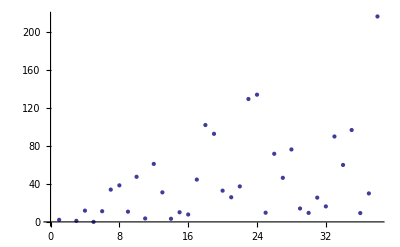

```mathematica
ListPlot[N[Log[%]]]
```

```mathematica
ToExpression[StringReplace[ToString[{{x->9}}],{"{{x -> "->"","}}"->""}]]
```

9

```mathematica
N[1/70,100]
```

0.01428571428571428571428571428571428571428571428571428571428571428571428571428571428571428571428571429

```mathematica
NestWhile[{#[[1]]/2,#[[2]]+1}&,{27890800,0},Mod[#[[1]],2]==0&]
```

{1743175,4}

```mathematica
NestWhile[{#[[1]]/5,#[[2]]+1}&,{27890800,0},Mod[#[[1]],5]==0&]
```

{1115632,2}

```mathematica
Piecewise[{{Solve[10^MultiplicativeOrder[10,b]-1==b x,x], GCD[x,10]==1}, {□, GCD[x,10]≠1}}]
```

```mathematica
Monitor[Table[Piecewise[{{MultiplicativeOrder[10,x], GCD[x,10]==1}, {Piecewise[{{Max[{(Piecewise[{{Last[NestWhile[{#[[1]]/5,#[[2]]+1}&,{x,0},Mod[#[[1]],5]==0&]], Mod[x,5]==0}, {0, Mod[x,5]≠0}}]),Last[NestWhile[{#[[1]]/2,#[[2]]+1}&,{x,0},Mod[#[[1]],2]==0&]]}], Mod[x,2]==0}, {Last[NestWhile[{#[[1]]/5,#[[2]]+1}&,{x,0},Mod[#[[1]],5]==0&]], Mod[x,2]≠0}}], GCD[x,10]≠1}}],{x,1,1000}],x]
```

{1,1,1,2,1,1,6,3,1,1,2,2,6,1,1,4,16,1,18,2,6,1,22,3,2,1,3,2,28,1,15,5,2,1,1,2,3,1,6,3,5,1,21,2,1,1,46,4,42,2,16,2,13,1,1,3,18,1,58,2,60,1,6,6,1,1,33,2,22,1,35,3,8,1,2,2,6,1,13,4,9,1,41,2,1,1,28,3,44,1,6,2,15,1,1,5,96,1,2,2,4,1,34,3,1,1,53,2,108,1,3,4,112,1,1,2,6,1,48,3,22,1,5,2,3,1,42,7,21,1,130,2,18,1,1,3,8,1,46,2,46,1,6,4,1,1,42,2,148,2,75,3,16,1,1,2,78,1,13,5,66,1,81,2,1,1,166,3,78,1,18,2,43,1,2,4,58,1,178,2,180,1,60,3,1,1,16,2,6,1,95,6,192,1,1,2,98,1,99,3,33,1,84,2,1,1,22,4,18,1,30,2,35,1,1,3,30,1,8,2,48,1,222,5,2,1,113,2,228,1,6,3,232,1,1,2,13,1,7,4,30,1,27,2,1,1,18,3,41,3,50,2,22,1,1,8,256,1,6,2,28,1,262,3,1,1,44,2,268,1,5,4,6,1,2,2,69,1,15,3,28,1,141,2,1,1,30,5,272,1,96,2,146,1,1,3,6,1,66,2,42,1,4,4,1,1,153,2,34,1,155,3,312,1,1,2,79,1,28,6,53,1,144,2,2,1,108,3,138,1,110,2,3,1,1,4,336,1,112,2,30,1,294,3,1,1,173,2,116,2,6,5,32,1,1,2,48,1,179,3,342,1,22,2,1,1,366,4,5,1,78,2,186,1,3,3,84,1,378,2,42,1,382,7,1,1,21,2,388,1,176,3,130,1,1,2,99,1,18,4,200,1,30,2,1,1,6,3,204,1,8,2,174,1,1,5,46,1,418,2,140,1,46,3,2,1,60,2,6,1,215,4,432,1,1,2,198,1,219,3,42,1,221,2,1,1,148,6,32,2,10,2,75,1,1,3,152,1,48,2,460,1,154,4,1,1,233,2,66,1,78,3,42,1,2,2,13,1,239,5,6,1,66,2,1,1,486,3,81,1,490,2,112,1,1,4,210,1,498,3,166,1,502,3,1,1,78,2,508,1,24,9,18,1,1,2,46,1,43,3,52,1,261,2,2,1,240,4,506,1,58,2,30,1,1,3,178,1,42,2,540,1,180,5,1,1,91,2,60,2,252,3,78,1,1,2,278,1,42,4,16,1,281,2,1,1,18,3,284,1,570,2,95,1,2,6,576,1,192,2,246,1,26,3,1,1,293,2,90,1,98,4,592,1,1,2,99,1,299,3,300,1,33,2,1,1,202,5,84,1,138,2,51,1,1,3,88,1,618,2,66,1,132,4,4,1,18,2,48,1,315,3,30,1,1,2,42,1,35,7,32,1,107,2,1,1,646,3,58,2,30,2,326,1,1,4,8,1,658,2,220,1,48,3,1,1,308,2,222,1,60,5,224,1,2,2,338,1,96,3,113,1,341,2,1,1,228,4,78,1,230,2,6,1,1,3,80,1,232,2,700,1,18,6,1,1,12,2,708,1,13,3,330,1,1,2,7,1,359,4,102,1,30,2,2,1,726,3,81,1,336,2,61,1,1,5,66,1,246,2,18,1,742,3,1,1,41,2,318,3,125,4,50,1,1,2,27,1,22,3,380,1,108,2,1,1,174,8,192,1,256,2,193,1,2,3,6,1,90,2,70,1,84,4,1,1,393,2,262,1,336,3,60,1,1,2,199,1,368,5,44,1,8,2,1,1,268,3,202,1,810,2,5,1,1,4,126,1,6,2,820,1,822,3,2,1,413,2,276,1,69,6,336,1,1,2,15,1,419,3,812,1,28,2,1,1,66,4,141,2,66,2,213,1,1,3,856,1,26,2,30,1,862,5,1,1,272,2,26,1,66,3,96,1,3,2,438,1,146,4,440,1,441,2,1,1,886,3,42,1,18,2,414,1,1,7,66,1,420,2,208,1,42,3,1,1,151,2,4,1,455,4,82,1,1,2,390,1,459,3,153,1,210,2,2,1,34,5,464,1,126,2,155,1,1,3,936,1,312,2,940,1,110,4,1,1,473,2,24,2,79,3,952,1,1,2,28,1,24,6,465,1,53,2,1,1,322,3,144,1,970,2,138,1,2,4,976,1,44,2,108,1,982,3,1,1,138,2,462,1,495,5,110,1,1,2,166,1,3,3}

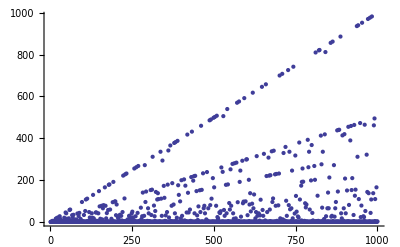

```mathematica
ListPlot[%]
```

```mathematica
Monitor[Table[Piecewise[{{MultiplicativeOrder[10,x], GCD[x,10]==1}, {0, GCD[x,10]≠1}}],{x,1,10000}],x]
```

{1,0,1,0,0,0,6,0,1,0,2,0,6,0,0,0,16,0,18,0,6,0,22,0,0,0,3,0,28,0,15,0,2,0,0,0,3,0,6,0,5,0,21,0,0,0,46,0,42,0,16,0,13,0,0,0,18,0,58,0,60,0,6,0,0,0,33,0,22,0,35,0,8,0,0,0,6,0,13,0,9,0,41,0,0,0,28,0,44,0,6,0,15,0,0,0,96,0,2,0,4,0,34,0,0,0,53,0,108,0,3,0,112,0,0,0,6,0,48,0,22,0,5,0,0,0,42,0,21,0,130,0,18,0,0,0,8,0,46,0,46,0,6,0,0,0,42,0,148,0,75,0,16,0,«9693»,0,462,0,9850,0,4814,0,0,0,9856,0,3286,0,774,0,96,0,0,0,66,0,1610,0,4935,0,1096,0,0,0,1968,0,132,0,30,0,4941,0,0,0,9886,0,420,0,78,0,1140,0,0,0,3298,0,468,0,12,0,3300,0,0,0,4953,0,366,0,208,0,4730,0,0,0,690,0,108,0,1653,0,4961,0,0,0,1102,0,1241,0,9930,0,42,0,0,0,522,0,3312,0,1988,0,1620,0,0,0,588,0,9948,0,795,0,804,0,0,0,553,0,4752,0,474,0,135,0,0,0,9966,0,1661,0,2262,0,554,0,0,0,302,0,4688,0,1108,0,4884,0,0,0,832,0,4278,0,1632,0,3330,0,0,0,192,0,4,0}

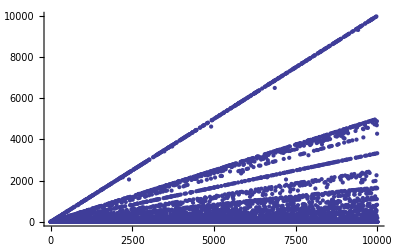

```mathematica
ListPlot[%]
```

```mathematica
Monitor[Table[Piecewise[{{0, GCD[x,10]==1}, {Piecewise[{{Max[{(Piecewise[{{Last[NestWhile[{#[[1]]/5,#[[2]]+1}&,{x,0},Mod[#[[1]],5]==0&]], Mod[x,5]==0}, {0, Mod[x,5]≠0}}]),Last[NestWhile[{#[[1]]/2,#[[2]]+1}&,{x,0},Mod[#[[1]],2]==0&]]}], Mod[x,2]==0}, {Last[NestWhile[{#[[1]]/5,#[[2]]+1}&,{x,0},Mod[#[[1]],5]==0&]], Mod[x,2]≠0}}], GCD[x,10]≠1}}],{x,1,1000}],x]
```

{0,1,0,2,1,1,0,3,0,1,0,2,0,1,1,4,0,1,0,2,0,1,0,3,2,1,0,2,0,1,0,5,0,1,1,2,0,1,0,3,0,1,0,2,1,1,0,4,0,2,0,2,0,1,1,3,0,1,0,2,0,1,0,6,1,1,0,2,0,1,0,3,0,1,2,2,0,1,0,4,0,1,0,2,1,1,0,3,0,1,0,2,0,1,1,5,0,1,0,2,0,1,0,3,1,1,0,2,0,1,0,4,0,1,1,2,0,1,0,3,0,1,0,2,3,1,0,7,0,1,0,2,0,1,1,3,0,1,0,2,0,1,0,4,1,1,0,2,0,2,0,3,0,1,1,2,0,1,0,5,0,1,0,2,1,1,0,3,0,1,0,2,0,1,2,4,0,1,0,2,0,1,0,3,1,1,0,2,0,1,0,6,0,1,1,2,0,1,0,3,0,1,0,2,1,1,0,4,0,1,0,2,0,1,1,3,0,1,0,2,0,1,0,5,2,1,0,2,0,1,0,3,0,1,1,2,0,1,0,4,0,1,0,2,1,1,0,3,0,3,0,2,0,1,1,8,0,1,0,2,0,1,0,3,1,1,0,2,0,1,0,4,0,1,2,2,0,1,0,3,0,1,0,2,1,1,0,5,0,1,0,2,0,1,1,3,0,1,0,2,0,1,0,4,1,1,0,2,0,1,0,3,0,1,1,2,0,1,0,6,0,1,0,2,2,1,0,3,0,1,0,2,0,1,1,4,0,1,0,2,0,1,0,3,1,1,0,2,0,2,0,5,0,1,1,2,0,1,0,3,0,1,0,2,1,1,0,4,0,1,0,2,0,1,3,3,0,1,0,2,0,1,0,7,1,1,0,2,0,1,0,3,0,1,1,2,0,1,0,4,0,1,0,2,1,1,0,3,0,1,0,2,0,1,1,5,0,1,0,2,0,1,0,3,2,1,0,2,0,1,0,4,0,1,1,2,0,1,0,3,0,1,0,2,1,1,0,6,0,2,0,2,0,1,1,3,0,1,0,2,0,1,0,4,1,1,0,2,0,1,0,3,0,1,2,2,0,1,0,5,0,1,0,2,1,1,0,3,0,1,0,2,0,1,1,4,0,1,0,3,0,1,0,3,1,1,0,2,0,1,0,9,0,1,1,2,0,1,0,3,0,1,0,2,2,1,0,4,0,1,0,2,0,1,1,3,0,1,0,2,0,1,0,5,1,1,0,2,0,2,0,3,0,1,1,2,0,1,0,4,0,1,0,2,1,1,0,3,0,1,0,2,0,1,2,6,0,1,0,2,0,1,0,3,1,1,0,2,0,1,0,4,0,1,1,2,0,1,0,3,0,1,0,2,1,1,0,5,0,1,0,2,0,1,1,3,0,1,0,2,0,1,0,4,4,1,0,2,0,1,0,3,0,1,1,2,0,1,0,7,0,1,0,2,1,1,0,3,0,2,0,2,0,1,1,4,0,1,0,2,0,1,0,3,1,1,0,2,0,1,0,5,0,1,2,2,0,1,0,3,0,1,0,2,1,1,0,4,0,1,0,2,0,1,1,3,0,1,0,2,0,1,0,6,1,1,0,2,0,1,0,3,0,1,1,2,0,1,0,4,0,1,0,2,2,1,0,3,0,1,0,2,0,1,1,5,0,1,0,2,0,1,0,3,1,1,0,2,0,3,0,4,0,1,1,2,0,1,0,3,0,1,0,2,1,1,0,8,0,1,0,2,0,1,2,3,0,1,0,2,0,1,0,4,1,1,0,2,0,1,0,3,0,1,1,2,0,1,0,5,0,1,0,2,1,1,0,3,0,1,0,2,0,1,1,4,0,1,0,2,0,1,0,3,2,1,0,2,0,1,0,6,0,1,1,2,0,1,0,3,0,1,0,2,1,1,0,4,0,2,0,2,0,1,1,3,0,1,0,2,0,1,0,5,1,1,0,2,0,1,0,3,0,1,3,2,0,1,0,4,0,1,0,2,1,1,0,3,0,1,0,2,0,1,1,7,0,1,0,2,0,1,0,3,1,1,0,2,0,1,0,4,0,1,1,2,0,1,0,3,0,1,0,2,2,1,0,5,0,1,0,2,0,1,1,3,0,1,0,2,0,1,0,4,1,1,0,2,0,2,0,3,0,1,1,2,0,1,0,6,0,1,0,2,1,1,0,3,0,1,0,2,0,1,2,4,0,1,0,2,0,1,0,3,1,1,0,2,0,1,0,5,0,1,1,2,0,1,0,3}

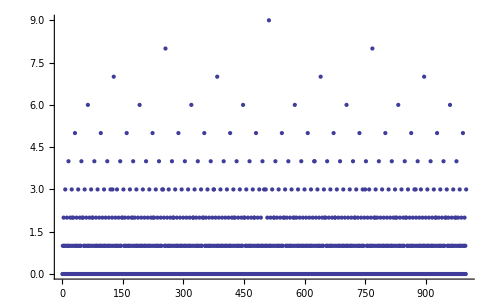

```mathematica
ListPlot[%]
```

```mathematica
Monitor[Table[MultiplicativeOrder[2,2x-1],{x,1,1000000}],x]
```

```mathematica
ListPlot[%]
```

```mathematica
Table[GCD[x,y],{x,1,100},{y,1,100}]//MatrixForm
```